# Radionchik_S_S Lab4: Работа с графикой

## 1. Общие правила работы с графикой. Вывод и манипуляции с объектами графики.

### 11.2а. Что следует вписать вместо Yaaaa для получения показанного ниже графика? -Graphics-

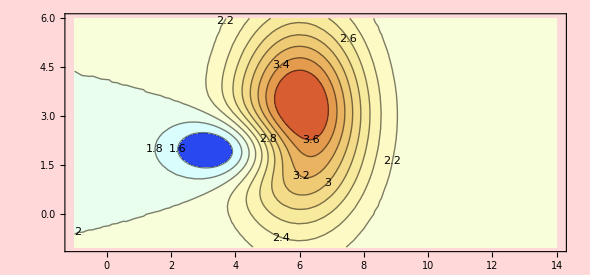

```mathematica
xmin:=-1;xmax:=14;
ymin:=-1;ymax:=6;
aspRat =(ymax-ymin)/(xmax-xmin);

fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2*E^(-(x/2-3)^2-(y/3-1)^2);
grf2Db=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11, ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,PlotRangePadding->{{1, 4}, {0, 2}},  (*отступ от границы графика*)Background->LightRed]
```

### 11.2b. Что следует вписать вместо Ybbbb для получения показанного ниже графика? -Graphics- -Graphics-

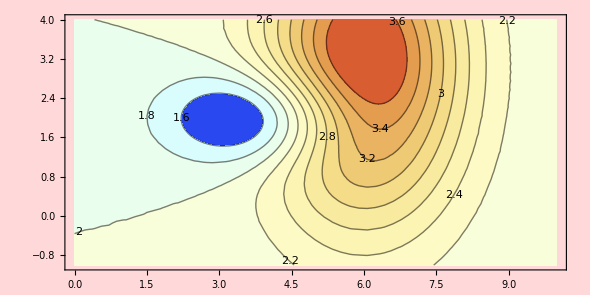

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat =(ymax-ymin)/(xmax-xmin);

fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2*E^(-(x/2-3)^2-(y/3-1)^2);
grf2Dc=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11, ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,PlotRegion->{{0.3,1}, {0,0.8}}, (*геометрический регион графика*)  Background->LightRed]
```

## 2. Функции Show, GraphicsShow

### 11.1c. Что следует вписать вместо Yccc для получения показанного ниже графика? -Graphics- -Graphics-

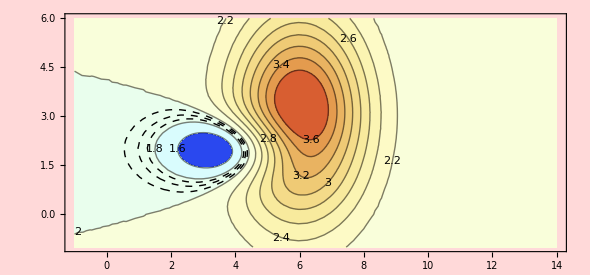

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat =(ymax-ymin)/(xmax-xmin);

fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2*E^(-(x/2-3)^2-(y/3-1)^2);
grf2Dd=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->{1.85,1.9,1.95},ContourStyle->Dashed,ContourShading->None, (*убрать оцвечивание контуров*)AspectRatio->aspRat,ImageSize->590];
Show[grf2Db,grf2Dd]
```

### 11.1d. Что следует вписать вместо Yddd для получения показанного ниже графика? -Graphics-

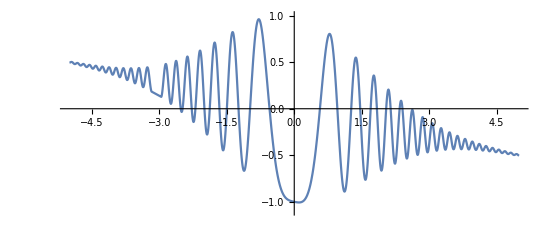

```mathematica
f3[x_] :=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
grf1DdFrgm=Plot[f3[x],{x,-4,-3},AspectRatio->3/7];
Plot[f3[x],{x,-5,5},AspectRatio->3/7,Epilog->Inset[grf1DdFrgm,Scaled[{0.05, .05}],Scaled[{0, 0}],4],(*вставка графика в эпилог*)PlotRange->{-1.1,1},PlotRangeClipping->False,ImageSize->550]
```

## 3. Цвет и его задание.

### 11.1e. Что следует вписать вместо Yeeee для получения показанного ниже графика справа? -Graphics-

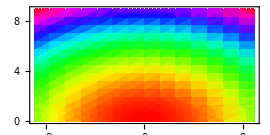
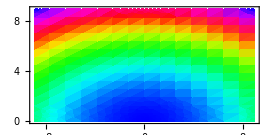

```mathematica
grf2Dd=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction->Hue,ImageSize->270];

grf2De=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction-> (Hue[2/3-#]&) (*тон оцвечивания, интуитивная цветовая модель Hue, 2/3 - синий*),ImageSize->270];
Row[{grf2Dd,grf2De},Spacer[5]]
```